# Cold Plasma Roots nz(nx) with Plasma Profiles

## Looking at Moiseenko and Agren, Physics of Plasmas 2005

## Open Additional files:

## Set Parameters by opening a Slab Parameter Window Get dispersion routines by evaluating Plasma_Dispersion.nb Get plotting and printing routines by evaluating PlotPack.nb

#### Plot Real and Imaginary parts of both roots nz from 2nd order in nz^2 cold plasma dispersion relation

### Define n-parallel module – N.B. this is nz^2

```mathematica
nParallel2FS[x_]:=Module[{ne,b,x0},x0=x;ne=nprof[x0];b=bprof[x0];nzColdDis2FS[freq,ne,b,nx,etaList]]
```

### Plot the roots vs B̄

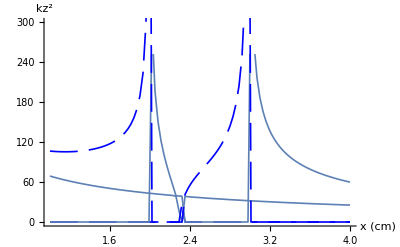

dataSet=nz(Bbar,nx) Moiseenko

xProfileMin=1.

xProfileMax=4.

nXmin=5.×10^20

nXmax=5.×10^20

BXmin=2.61768

BXmax=10.4707

freq=39.7887

nx=3.

etaList={0.,0.4,0.6,0.,0.}

xmin=1.

xmin=1.

```mathematica
nt2FS=Table[Flatten[{x,k0^2 nParallel2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=myComplexListPlot[nF,"x (cm)","kz^2"];
g2=myComplexListPlot[nS,"x (cm)","kz^2 (m^-1)"];
Show[{g1,g2},PlotRange->{0,300}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nx,etaList,xmin,xmin}];
```

#### Zoom in on mode conversion region

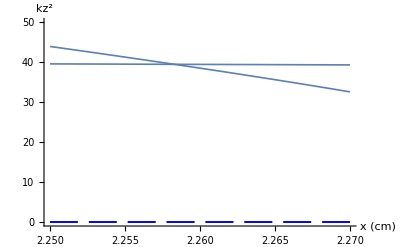

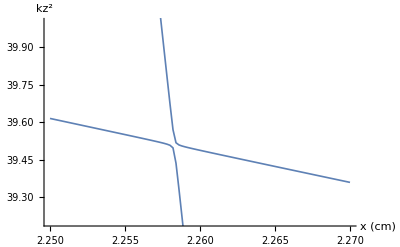

dataSet=nz(Bbar,nx) Moiseenko

xProfileMin=2.25

xProfileMax=2.27

nXmin=5.×10^20

nXmax=5.×10^20

BXmin=5.88978

BXmax=5.94213

freq=39.7887

nx=3.

etaList={0.,0.4,0.6,0.,0.}

xmin=2.25

xmin=2.25

```mathematica
nt2FS=Table[Flatten[{x,k0^2  nParallel2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=myComplexListPlot[nF,"x (cm)","kz^2"];
g2=myComplexListPlot[nS,"x (cm)","kz^2 (m^-1)"];
Show[{g1,g2},PlotRange->{0,50}]
Show[{g1,g2},PlotRange->{39.2,40.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nx,etaList,xmin,xmin}];
```

## Initialization

```mathematica
Needs["`PlotPack`"]
```

Get::noopen: Cannot open Global`PlotPack`.

Needs::nocont: Context Global`PlotPack` was not created when Needs was evaluated.

$Failed

Magnetic field, Density and Temperature Profiles

#### Magnetic field, and Density Profiles – both linear

```mathematica
bprof[x_]:=If[Abs[(BXmax-BXmin)/BXmax]>10^-6,BXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(BXmax-BXmin),BXmin];
```

```mathematica
nprof[x_]:=If[Abs[(nXmax-nXmin)/nXmax]>10^-6,nXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(nXmax-nXmin),nXmin];
```